```mathematica
(* clear memory *)
ClearAll["Global`*"]
```

```mathematica
(* Declare TDOS function that take the eigenvalue list and Gaussian width as inputs and returns TDOS as a function of energy *)
TDOS[Energy_,Eigenvalues_,Gwidth_]:=Apply[Plus,1/(Sqrt[2Pi]Gwidth)Exp[-(Energy-Eigenvalues)^2/(2 Gwidth^2)]];
```

```mathematica
(* Read orbital eigenvalues, in this example MOs.txt have three columns. If it contains more or less columns, change the size of the array in the second argument *)
Data1=ReadList["/home/zhenzhe/Desktop/mols_MOs/Azulene-3-MOs.txt",{Number,Number,Number,String}];
Data2=ReadList["/home/zhenzhe/Desktop/mols_MOs/Graphene-3-MOs.txt",{Number,Number,Number,String}];
(* Use the second column *)
(*Data1*)
OrbitalEnergies=Data1[[All,3]];
OrbitalEnergies2=Data2[[All,3]];
(*OrbitalEnergiesz*)
Length[OrbitalEnergies]
Length[OrbitalEnergies2]
OrbitalEnergies=OrbitalEnergies*27.2114
OrbitalEnergies2=OrbitalEnergies2*27.2114
```

1174

1177

{663.095,662.847,662.847,662.57,662.57,662.291,662.09,661.725,661.725,661.616,661.616,661.46,660.452,660.258,660.256,659.831,659.829,659.751,658.065,657.594,657.593,657.096,657.052,657.05,656.874,656.691,656.691,656.337,656.336,655.989,654.852,654.422,654.422,654.194,653.747,653.747,652.739,652.739,652.12,652.12,651.665,651.627,651.197,648.601,648.6,644.371,644.371,640.677,137.968,136.275,136.274,135.56,135.56,134.77,134.481,132.35,132.102,132.102,132.04,131.885,131.885,129.494,129.493,123.867,123.867,122.888,120.808,119.995,119.994,119.271,118.882,118.882,118.421,118.386,118.385,116.562,116.562,114.614,113.904,113.542,113.513,113.512,113.477,113.477,107.874,107.873,107.26,107.26,106.736,105.162,104.949,104.237,103.744,103.744,103.2,103.2,102.741,102.741,102.557,102.557,102.465,102.272,101.587,101.077,101.077,101.04,101.03,101.03,99.6816,99.6813,99.4217,99.4212,99.3978,99.2917,98.6185,98.4609,98.4609,98.1224,98.1224,97.92,96.3673,95.4481,95.4141,95.4138,94.9863,94.986,94.9588,94.1612,94.161,94.0091,93.9199,93.9196,93.4423,93.2886,93.2883,93.22,93.2195,93.0668,92.7612,92.7607,92.6692,92.6692,92.6578,91.6817,91.4687,91.2064,90.8425,90.8425,90.8414,90.8412,89.1505,88.366,88.3658,87.4961,87.4033,87.4033,87.3168,86.9744,86.6585,86.6582,86.6503,86.6381,86.6381,86.1937,86.1935,85.8297,85.6803,85.6803,85.5654,85.4868,85.4857,85.4811,85.4647,85.059,84.9643,84.9643,84.807,84.807,84.3864,84.3858,84.3553,84.3553,83.8329,83.5523,83.1589,83.158,83.108,83.108,82.6799,82.6797,82.5262,82.0791,81.9235,81.9235,81.3507,81.3498,81.3117,81.3115,81.2486,81.0219,80.5732,80.1392,79.6216,79.6206,79.6203,79.5509,79.4295,79.4295,79.1528,79.1163,79.0856,79.0856,78.9163,78.9161,78.8094,78.8091,78.672,78.672,78.5449,78.4807,78.3729,78.3729,78.0736,78.0733,77.8869,77.8461,77.8458,77.7394,77.7394,77.4183,77.3266,77.3266,77.2605,77.1479,77.1245,77.008,77.0077,76.9204,76.6088,76.5277,76.5277,76.4156,76.4153,76.0877,76.0118,76.0115,75.9266,75.3448,75.3427,75.1122,74.6409,74.6409,74.6262,74.6254,74.3824,74.3821,74.2014,74.2014,74.1475,73.9609,73.5794,73.5116,73.5102,73.3891,72.2577,71.7518,71.7516,71.4269,71.1619,71.1619,70.9676,70.7211,70.6881,70.6881,70.5393,70.539,70.4408,70.4405,70.1763,69.1687,69.1684,68.9284,68.352,68.3515,68.1703,67.9665,67.9659,67.7052,67.3939,66.8595,66.859,66.6647,66.3354,65.6249,65.6249,65.4627,65.4625,65.288,65.2878,65.18,65.0703,64.8105,64.8105,64.777,64.777,64.4088,64.2679,64.2673,63.9539,63.5419,63.3201,63.3201,63.0872,63.0872,62.888,62.8875,62.8355,62.7438,62.7438,62.4986,62.2605,62.26,61.8893,61.6657,61.3846,61.3769,60.9182,60.9182,60.6961,60.6956,59.913,59.9051,59.9048,59.6523,59.5965,59.5962,59.446,59.314,59.1611,59.1611,59.1497,58.8958,58.8955,58.877,58.8768,58.7393,58.5146,58.514,58.1195,58.1195,57.6365,57.6359,57.4136,57.0854,57.0852,57.0354,56.8656,56.6598,56.6596,56.5646,56.4873,56.4873,56.3137,56.3134,56.2013,55.945,55.945,55.933,55.8691,55.7583,55.4013,55.401,55.0868,54.9918,54.9915,54.8557,54.6212,54.6005,54.6002,54.3586,54.2639,54.2633,54.105,53.9733,53.973,53.9123,53.4756,53.4753,53.2949,53.2946,53.164,53.1637,52.4644,52.4287,52.1732,52.1732,51.743,51.7427,51.4818,51.2842,51.1993,51.1991,51.1748,51.1095,50.8448,50.8445,50.7746,50.7746,50.7528,50.7523,50.5248,50.5248,50.3713,50.2741,50.18,50.1348,50.1188,50.109,50.1087,49.9759,49.9759,49.4447,49.4439,49.3642,49.3642,49.1822,49.1607,48.3416,48.2981,48.2975,47.8921,47.8921,47.7854,47.719,47.5555,47.5555,47.5516,47.5514,47.5296,47.2765,47.1446,47.1446,46.7565,46.4161,46.4161,46.1029,46.1029,46.015,45.6406,45.6406,45.5919,45.5919,45.5894,45.5864,45.5862,45.5598,45.5372,45.535,45.535,45.0234,45.0232,44.8901,44.8574,44.7611,44.7608,44.6188,44.6188,44.3608,43.8618,43.7241,43.7012,43.7007,43.2509,43.2509,42.742,42.729,42.729,42.4228,42.3777,42.3774,42.3475,42.3475,42.3369,42.1499,42.1499,42.1377,42.0416,41.4824,41.4821,41.3061,41.3058,41.2255,41.2253,41.0127,40.8552,40.8552,40.69,40.2859,39.776,39.7518,38.6048,38.5044,38.5044,38.4881,38.4875,37.4513,37.4513,37.1637,36.8853,36.8263,36.826,36.6197,36.6197,36.6029,36.4635,36.4633,36.4554,36.3952,35.8584,35.8584,35.8284,35.8284,34.8483,34.528,34.5277,34.356,34.3558,34.236,34.2026,33.6695,33.6031,33.6031,33.3797,33.3797,33.1854,33.1854,33.1764,33.1372,32.9514,32.9511,32.7748,32.704,32.6942,32.5821,32.5821,32.5105,32.5103,32.125,32.125,31.9726,31.4986,31.4983,31.4273,31.4194,31.3339,31.282,31.2817,31.1266,31.1263,31.1005,31.1002,31.0632,31.0632,30.7824,30.6964,30.6961,30.6321,30.5241,30.5241,30.4327,30.1236,29.9981,29.9968,29.9968,29.8678,29.8678,29.8335,29.7984,29.7772,29.7772,29.7559,29.7559,29.6906,29.5206,29.4953,29.0495,29.0495,28.9897,28.9891,28.9657,28.8893,28.8893,28.766,28.6895,28.6893,28.5309,28.5129,28.4199,28.4196,28.3377,28.3374,28.2286,28.2286,28.2128,28.2125,28.0642,28.0574,27.9379,27.8631,27.8174,27.8171,27.7575,27.7575,27.5828,27.5828,27.342,27.342,27.2487,27.2484,27.1836,27.0846,27.0128,27.0125,26.4693,26.4084,26.2808,26.2808,26.2459,26.1583,25.8612,25.8612,25.8435,25.8435,25.4971,25.4971,25.0856,24.5697,24.5586,24.5583,24.5341,23.9139,23.9019,23.9019,23.7768,23.7768,23.7634,23.6902,23.62,23.62,23.4489,23.4489,23.1419,23.0674,23.0671,23.0633,23.063,22.7406,22.7248,22.7248,22.7087,22.7087,22.6072,22.6072,22.5694,22.5694,22.5629,22.5144,22.5142,22.4519,22.4513,22.398,22.2989,22.1231,22.1231,22.0271,21.6701,21.6295,21.5716,21.528,21.528,21.374,21.2853,21.1588,20.9871,20.9313,20.931,20.8102,20.8099,20.7835,20.445,20.4447,20.3152,20.3152,20.1253,20.1253,20.1182,20.0227,20.0224,19.7655,19.7655,19.7606,19.5062,19.5059,19.4336,19.4327,19.3421,19.3059,19.2556,19.1595,19.1078,19.1076,19.0907,19.0904,18.8771,18.8768,18.8657,18.8412,18.827,18.7889,18.6956,18.6953,18.5731,18.4112,18.4112,18.3157,18.2719,18.2716,18.2632,18.2632,18.1168,18.0248,18.0248,18.0096,17.7277,17.7277,17.5611,17.5611,17.4077,17.3984,17.3982,17.3032,17.3029,17.289,17.0036,16.9922,16.981,16.981,16.8406,16.8403,16.7625,16.6871,16.6866,16.5249,16.5249,16.5228,16.409,16.409,15.9935,15.9935,15.8566,15.8512,15.5804,15.5804,15.523,15.4449,15.1562,14.9774,14.9774,14.9249,14.9249,14.5842,14.5839,14.5807,14.3589,14.3589,14.1937,14.0607,13.8762,13.8511,13.7676,13.7676,13.7635,13.7635,13.5301,13.3298,13.3298,13.154,13.0386,13.0386,13.0223,13.022,12.8079,12.7344,12.7341,12.683,12.5815,12.5085,12.5085,12.4933,12.4228,12.4228,12.0361,12.0359,11.9292,11.7327,11.7327,11.6231,11.5447,11.4519,11.192,11.192,11.115,11.0584,11.0584,11.035,11.0348,10.8299,10.8296,10.7684,10.708,10.5844,10.5684,10.5684,10.561,10.561,10.5599,10.5599,10.5572,10.5569,10.5463,10.3058,10.3058,10.2854,10.2734,10.269,10.2688,9.88617,9.88617,9.8557,9.72916,9.6625,9.61814,9.61814,9.60943,9.60943,9.59664,9.59664,9.54304,9.19664,9.19636,9.15391,9.14956,9.03527,9.03527,9.00752,8.98901,8.98874,8.76071,8.76044,8.69704,8.68833,8.55962,8.53513,8.53486,8.48234,8.41812,8.38519,8.37676,8.37676,8.26737,8.2671,8.0894,8.0894,8.05403,8.05376,8.00206,7.88287,7.86328,7.86192,7.86192,7.84396,7.84369,7.82164,7.82164,7.76368,7.63334,7.63307,7.49239,7.49239,7.28694,7.25891,7.17429,7.16503,7.16503,7.01673,7.01646,6.93863,6.93863,6.93074,6.87061,6.86761,6.83197,6.83197,6.79877,6.79088,6.74652,6.74625,6.62298,6.62298,6.60013,6.60013,6.56312,6.56257,6.52094,6.47522,6.45046,6.43713,6.43713,6.28855,6.19168,6.19168,6.08529,6.06161,6.06161,6.03685,5.99658,5.99658,5.87957,5.87957,5.77072,5.70569,5.70569,5.64092,5.60936,5.60909,5.4967,5.4967,5.48146,5.39112,5.30432,5.30405,5.21207,5.19874,5.19085,5.19085,5.06812,5.01805,4.89751,4.89751,4.88553,4.88553,4.76009,4.75982,4.70322,4.68335,4.68335,4.58213,4.46185,4.46185,4.24471,4.24471,4.24008,4.14294,4.14294,4.08797,4.08797,4.08525,4.0564,3.98157,3.95599,3.95599,3.76987,3.76987,3.7198,3.7198,3.70728,3.66701,3.44279,3.20169,3.1353,3.1353,3.0523,3.0523,2.99734,2.99734,2.93448,2.93448,2.8659,2.75978,2.64685,2.58536,2.41229,2.32195,2.32168,2.15786,2.15786,1.78616,1.78616,1.7165,1.71622,1.51105,1.42125,1.37145,1.37037,1.37009,1.35404,1.23649,1.23649,1.0939,1.0939,1.01934,0.520826,0.519194,-0.58314,-0.753212,-0.753484,-1.54044,-1.54044,-6.78026,-6.78026,-6.88204,-6.88204,-7.95117,-8.37757,-8.60424,-9.58957,-9.95883,-9.9591,-10.3289,-10.3292,-11.1575,-11.1575,-11.327,-11.327,-11.3719,-11.3915,-11.3915,-11.4829,-11.5776,-11.8389,-11.8391,-12.0734,-12.1597,-12.179,-12.2917,-12.2917,-12.3804,-12.3804,-12.8065,-12.92,-12.92,-13.1045,-13.1409,-13.1409,-13.2631,-13.2783,-13.2786,-13.3831,-13.3831,-13.413,-13.8261,-13.8264,-13.9526,-13.9526,-14.1627,-14.3135,-14.5633,-14.6786,-14.6789,-14.7562,-15.0182,-15.0182,-15.1665,-15.6101,-15.6101,-15.7598,-15.76,-15.7842,-16.1018,-16.3328,-16.3331,-16.5494,-16.5497,-16.8447,-17.2537,-17.2537,-17.8814,-17.9905,-17.9933,-17.9933,-18.9506,-18.9508,-18.9702,-19.1933,-19.1933,-19.6741,-19.9892,-20.0627,-20.5759,-20.5759,-21.0703,-21.0703,-21.9147,-21.9147,-22.2535,-22.2535,-22.7389,-23.078,-23.6312,-23.7177,-24.2688,-24.2688,-24.3458,-24.3458,-24.8563,-24.8563,-25.0386,-25.1915,-25.1915,-25.6024,-26.8108,-27.0879,-27.0879,-27.4536,-27.4536,-27.5986,-279.766,-279.766,-279.766,-279.766,-279.766,-279.766,-280.412,-280.412,-280.412,-280.412,-280.412,-280.412,-280.422,-280.422,-280.422,-280.422,-280.422,-280.422,-280.474,-280.474,-280.474,-280.474,-280.474,-280.474,-280.493,-280.493,-280.493,-280.493,-280.493,-280.493,-280.56,-280.56,-280.56,-280.56,-280.56,-280.56,-280.56,-280.56,-280.56,-280.56,-280.56,-280.56,-280.943,-280.943,-280.943,-280.944,-280.944,-280.944}

{662.983,662.916,662.819,662.817,662.8,662.798,662.029,661.557,661.556,661.535,661.534,661.374,660.251,659.743,659.741,659.441,659.44,659.372,658.,657.753,657.753,657.59,657.59,657.434,656.588,656.335,656.335,656.122,656.121,655.942,655.685,655.59,655.59,655.027,655.025,654.602,652.933,652.932,652.877,652.554,652.553,651.944,651.062,648.888,648.888,644.654,644.653,640.446,139.116,136.514,136.514,136.436,135.769,135.769,134.828,134.467,134.216,134.216,133.684,133.684,132.991,130.232,130.231,124.711,124.062,124.061,120.679,120.676,119.958,119.546,119.279,119.277,118.352,118.351,117.76,117.476,117.475,116.244,114.841,114.096,114.096,113.812,113.768,113.768,108.834,108.833,108.634,108.632,107.559,107.101,106.491,105.959,105.066,105.066,104.96,104.96,104.606,104.18,104.18,103.132,103.131,102.57,102.406,102.405,102.251,102.25,102.247,101.348,100.584,99.9477,99.8873,99.8868,99.3703,99.3698,99.1616,99.1613,98.7268,98.3047,98.2868,98.0198,98.0193,97.373,97.1257,96.8565,96.8552,96.8367,96.8358,95.961,95.9607,95.8402,95.8396,95.3572,95.3419,95.0549,95.0546,94.4451,94.4445,93.7634,92.589,92.3593,92.359,92.1226,92.122,91.8241,91.8219,91.6804,91.1966,91.1966,91.1321,90.3818,90.3818,90.1247,90.1244,89.8175,89.7247,89.3222,89.0724,88.0879,87.9687,87.9685,87.8188,87.8183,87.5663,87.2193,86.772,86.7676,86.7235,86.7235,86.6139,86.1701,86.1684,86.055,85.889,85.889,85.4188,85.1548,85.0718,84.2443,84.2438,84.1499,84.1496,83.9776,83.9768,82.5724,82.232,82.2318,82.1915,82.1912,81.7975,81.7975,81.5825,81.5817,81.2619,81.189,81.189,81.1509,80.8492,80.7776,80.6032,80.4949,80.4946,80.4679,80.4668,80.4116,80.3735,79.7305,79.512,79.5117,79.4921,79.1778,79.1599,79.158,79.0461,79.0456,79.0306,78.9536,78.9536,78.7563,78.7561,78.6396,78.5732,78.5724,78.555,78.5547,78.3375,78.3367,78.1,78.0388,77.5985,77.5982,77.4975,77.4975,77.4755,77.4096,77.4096,77.3732,77.1718,77.0703,76.8744,76.8741,76.7715,76.7715,76.5525,76.4804,76.4801,76.1288,75.4123,74.962,74.9573,74.8428,74.8428,74.602,74.596,74.439,74.439,74.3271,74.3026,74.2999,74.0572,73.9976,73.9445,73.9443,73.6253,73.1559,73.0795,72.849,72.6468,72.6463,72.4207,72.4201,70.8242,70.151,70.1409,70.139,70.1009,70.0928,70.0922,69.5926,69.5689,69.5687,68.8838,68.8835,68.8391,68.8391,68.8043,68.6231,68.0905,68.0897,67.2494,67.2473,66.9194,66.8004,66.7999,66.5351,66.5346,65.9264,65.9261,65.5196,65.4162,65.3514,65.3514,64.9838,64.9838,64.962,64.0856,64.0853,64.0565,64.0086,63.9005,63.8086,63.8083,63.78,63.3288,62.965,62.9615,62.904,62.7087,62.3974,62.3952,61.7095,61.7095,61.3353,61.0461,60.9214,60.9163,60.787,60.7854,60.7503,60.6866,60.6148,60.6139,60.3952,59.6411,59.6411,59.4749,59.4746,59.277,59.2398,59.2387,58.9249,58.9249,58.9143,58.9138,58.877,58.877,58.5902,58.5301,58.2289,57.9834,57.9834,57.7597,57.7595,57.2569,57.2547,57.0639,57.0631,56.9801,56.9801,56.9518,56.7913,56.7907,56.665,56.4879,56.4868,56.0438,56.0432,55.7662,55.766,55.7333,55.7137,55.333,55.3325,55.3303,55.33,55.1077,54.9578,54.9575,54.905,54.9042,54.7208,54.6146,54.5311,54.4979,54.3246,54.3199,53.9836,53.5909,53.5907,53.4465,53.3052,53.1469,53.1207,52.896,52.8745,52.8742,52.5743,52.5735,52.3411,52.3411,52.336,52.2445,52.2429,52.0459,52.0448,51.884,51.8832,51.4576,51.4576,50.9996,50.9977,50.524,50.3177,50.3174,50.3144,50.3139,50.2826,50.278,50.195,49.8475,49.8461,49.4094,49.4086,49.2066,49.1237,49.1231,48.9966,48.9302,48.7838,48.6341,48.6338,48.5204,48.5204,48.2153,47.43,47.2447,47.0376,47.0376,46.8665,46.5816,46.5813,46.4167,46.4164,46.1146,46.1143,46.1073,46.0518,46.0512,45.8085,45.8082,45.7497,45.7494,45.501,45.4999,45.4806,45.3083,44.916,44.572,44.572,44.4928,44.4474,44.4463,44.3551,44.3549,44.3091,44.3091,44.2275,44.0264,44.0261,43.6928,43.6928,43.6901,43.5801,43.3135,43.1856,43.1853,43.0128,42.8658,42.8656,42.7271,42.449,42.4487,42.3894,42.3891,42.366,42.3657,42.3069,42.3069,42.274,41.9886,41.8939,41.8299,41.8201,41.8198,41.8177,41.8171,41.7124,41.711,41.607,41.407,41.4054,41.2492,41.2489,41.1597,40.9581,40.9044,40.8908,39.9518,39.9518,38.9967,38.6709,38.1689,38.1681,38.1185,38.1169,37.6685,37.5955,37.595,36.6312,35.959,35.9582,35.5593,35.5588,35.1288,35.1286,34.8736,34.7016,34.7013,34.657,34.4104,34.1255,34.1255,34.0635,34.0632,33.9201,33.9187,33.8553,33.8545,33.845,33.8172,33.817,33.7351,33.7277,33.307,33.1443,32.9195,32.8899,32.3135,32.3135,32.2352,32.2349,31.9467,31.9465,31.7255,31.7244,31.5864,31.5304,31.5298,31.5252,31.5252,31.2131,31.2128,31.1976,31.,30.8509,30.8509,30.8504,30.7323,30.732,30.6874,30.6292,30.4153,30.2504,30.231,30.2166,30.1647,30.1644,30.1464,30.077,30.0765,29.6792,29.584,29.584,29.4719,29.4716,29.4144,29.4144,29.16,29.1597,29.1404,29.1404,29.009,28.8346,28.8346,28.7249,28.7246,28.6694,28.4658,28.4103,28.4101,28.3565,28.3556,28.2245,28.2245,28.1916,28.0637,28.0634,28.0084,27.9809,27.9807,27.9412,27.9409,27.7393,27.739,27.7175,27.6424,27.573,27.5728,27.5409,27.4857,27.2326,27.2324,27.1845,27.1842,27.1515,27.1513,27.0732,26.9325,26.8473,26.3746,26.33,26.1295,25.7948,25.7948,25.5409,25.5409,24.9814,24.8549,24.6829,24.5928,24.592,24.4897,24.3531,24.3528,24.2443,23.9928,23.9926,23.8913,23.8905,23.6304,23.6105,23.6102,23.4062,23.4062,23.3773,23.3768,23.256,23.2277,23.2274,23.189,23.1594,23.0671,22.9928,22.9925,22.8821,22.8815,22.8483,22.8483,22.7683,22.7289,22.7286,22.6225,22.5147,22.5147,22.3357,22.1923,22.192,21.8203,21.7188,21.6687,21.6687,21.6135,21.6129,21.2477,21.0543,20.9392,20.872,20.6608,20.6608,20.4758,20.4752,20.4749,20.4551,20.3598,20.3598,20.2398,20.2396,20.1868,20.1868,20.0812,20.0793,20.079,20.0028,20.0023,19.9166,19.7909,19.67,19.67,19.4417,19.4415,19.3976,19.2695,19.2692,19.2518,19.184,19.1642,19.1283,19.1283,19.064,19.0178,19.0175,18.9209,18.9206,18.5761,18.4961,18.4961,18.4613,18.3184,18.3184,18.2115,18.1944,18.1941,18.0803,18.0803,17.9236,17.8139,17.8134,17.7816,17.6681,17.6678,17.5514,17.5511,17.2137,17.2137,17.2118,17.1386,17.101,17.101,17.0504,16.9481,16.9454,16.7054,16.701,16.59,16.59,16.5434,16.5434,16.4109,16.209,16.209,16.1957,16.1568,16.1568,16.0145,15.8993,15.8738,15.6615,15.6215,15.6212,15.5562,15.5559,15.3475,15.3475,15.077,15.0767,14.6599,14.6444,14.5355,14.5143,14.514,14.5113,14.5113,14.3524,14.1894,14.1235,14.1235,13.8514,13.8514,13.6427,13.5322,13.5317,13.4005,13.0334,13.0334,13.025,13.0103,13.0103,12.8658,12.8658,12.8285,12.7355,12.5828,12.5828,12.2639,12.2604,12.2419,12.2416,11.7782,11.696,11.6957,11.5417,11.3934,11.3931,11.2386,11.2383,11.2174,10.8203,10.7471,10.7469,10.745,10.7447,10.6742,10.6742,10.5512,10.493,10.416,10.3825,10.3822,10.379,10.3591,10.3591,10.3305,10.3305,10.3224,10.3224,10.0386,9.93788,9.93788,9.87311,9.87284,9.80835,9.80808,9.79039,9.77488,9.66005,9.66005,9.52236,9.50739,9.4829,9.4829,9.37732,9.37732,9.29242,9.23664,9.2233,9.15065,9.15065,9.12915,9.02248,9.00208,9.00208,8.93922,8.93894,8.80126,8.7237,8.72343,8.70928,8.67146,8.67118,8.65867,8.56669,8.56642,8.55771,8.49349,8.469,8.469,8.43907,8.43907,8.27308,8.27281,8.20832,8.07961,8.05539,8.05539,8.05185,8.05158,7.94165,7.93348,7.81539,7.81539,7.74654,7.74654,7.70899,7.70845,7.69157,7.5479,7.48531,7.48504,7.40068,7.40068,7.2151,7.20912,7.19551,7.19497,7.13292,7.13292,6.97047,6.97047,6.91578,6.91551,6.86272,6.78924,6.74108,6.74081,6.71523,6.71523,6.67087,6.51441,6.48339,6.48312,6.37481,6.33019,6.32339,6.23114,6.18243,6.18216,6.04746,6.04637,6.01889,6.01862,5.92583,5.92583,5.81453,5.73807,5.7378,5.72609,5.59711,5.35357,5.35275,5.35275,5.31738,5.27166,5.245,5.24473,5.2284,4.9922,4.95111,4.95111,4.94594,4.94594,4.86594,4.81397,4.80417,4.80417,4.73805,4.73805,4.58512,4.58512,4.47111,4.47111,4.41233,4.39274,4.32335,4.32335,4.31709,4.31709,4.12606,4.11817,4.10729,4.10729,4.00906,4.00906,3.84688,3.84688,3.82429,3.7217,3.68007,3.68007,3.65667,3.55626,3.55626,3.46238,3.1206,3.1206,3.03353,3.03325,2.97856,2.97856,2.97366,2.79298,2.79298,2.78645,2.71352,2.66971,2.5878,2.53338,2.37365,2.37338,2.16684,2.16684,2.07732,2.07705,1.88765,1.88765,1.79323,1.79323,1.59921,1.47622,1.46533,1.45663,1.2403,1.2403,1.08247,1.08247,1.01635,0.888452,0.653074,0.289529,-0.312115,-0.312387,-0.459328,-0.459328,-7.34789,-7.34789,-7.59389,-7.59389,-8.34546,-8.68425,-8.79527,-9.18956,-9.91202,-9.91202,-10.2026,-10.2029,-11.0157,-11.016,-11.0508,-11.0511,-11.0794,-11.2329,-11.2982,-11.2982,-11.4323,-11.4329,-11.5782,-11.8024,-12.3295,-12.3298,-12.3719,-12.3744,-12.4391,-12.6533,-12.6533,-13.1562,-13.1562,-13.33,-13.33,-13.4103,-13.4106,-13.7007,-13.7526,-13.7529,-13.8419,-13.8615,-13.9584,-13.9586,-14.0359,-14.0362,-14.058,-14.1839,-14.2762,-14.5026,-14.5026,-14.6188,-14.6555,-15.015,-15.0158,-15.2966,-15.2966,-15.384,-15.3842,-15.4716,-16.3573,-16.3573,-16.3984,-16.6634,-16.6637,-16.9497,-16.9497,-17.0999,-17.6311,-18.0052,-18.0052,-18.1919,-18.978,-19.0872,-19.0874,-19.2112,-19.463,-19.4635,-19.6763,-20.4412,-20.4412,-20.5465,-20.5762,-20.5762,-22.1781,-22.1784,-22.2135,-22.2135,-23.0151,-23.1463,-23.1485,-23.447,-24.1088,-24.109,-24.1433,-24.1433,-24.8233,-24.8233,-24.9744,-25.2862,-25.2865,-26.1355,-26.1638,-26.8743,-26.8743,-27.3676,-27.3676,-27.5458,-280.155,-280.155,-280.155,-280.156,-280.156,-280.156,-280.245,-280.245,-280.245,-280.245,-280.245,-280.245,-280.265,-280.265,-280.265,-280.265,-280.265,-280.265,-280.267,-280.267,-280.267,-280.267,-280.267,-280.267,-280.492,-280.492,-280.492,-280.493,-280.493,-280.493,-280.495,-280.496,-280.496,-280.496,-280.496,-280.496,-280.506,-280.506,-280.506,-280.506,-280.506,-280.506,-280.512,-280.512,-280.512,-280.512,-280.512,-280.513}

```mathematica
GaussWidth=0.2;
TDOS1=TDOS[Ex,OrbitalEnergies,GaussWidth];
(* TDOS1 is now a smooth function of Ex *)

TDOS2=TDOS[Ex,OrbitalEnergies2,GaussWidth];
```

General::munfl: Exp[-5.83272×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5.82849×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

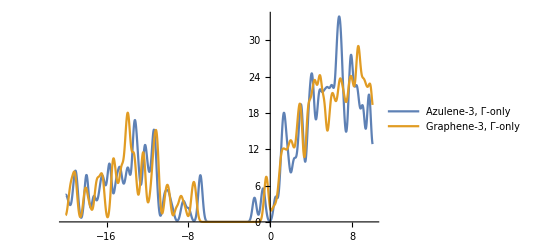

```mathematica
(* Plot two DOS functions. They are the same in this example *)
Emin=-20;
Emax=10;
Plot1=Plot[{TDOS1,TDOS2},{Ex,Emin,Emax},PlotRange->All,PlotLegends->{"Azulene-3, Γ-only","Graphene-3, Γ-only"}]
```